```mathematica
sx={{0,1},{1,0}}/2
```

{{0,1/2},{1/2,0}}

```mathematica
sy={{0,-I},{I,0}}/2
```

{{0,-ⅈ/2},{ⅈ/2,0}}

```mathematica
sz={{1,0},{0,-1}}/2
```

{{1/2,0},{0,-1/2}}

```mathematica
e= {{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
{{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
z={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
Sza = TensorProduct[sz,e]//ArrayFlatten
```

{{1/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-1/2}}

```mathematica
Szb= TensorProduct[e, sz]//ArrayFlatten
```

{{1/2,0,0,0},{0,-1/2,0,0},{0,0,1/2,0},{0,0,0,-1/2}}

```mathematica
Sxa=TensorProduct[sx,e]//ArrayFlatten
```

{{0,0,1/2,0},{0,0,0,1/2},{1/2,0,0,0},{0,1/2,0,0}}

```mathematica
Sxb= TensorProduct[e, sx]//ArrayFlatten
```

{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,1/2},{0,0,1/2,0}}

```mathematica
Sya=TensorProduct[sy,e]//ArrayFlatten
```

{{0,0,-ⅈ/2,0},{0,0,0,-ⅈ/2},{ⅈ/2,0,0,0},{0,ⅈ/2,0,0}}

```mathematica
Syb= TensorProduct[e, sy]//ArrayFlatten
```

{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0}}

```mathematica
EE= TensorProduct[e, e]/2//ArrayFlatten
```

{{1/2,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,1/2}}

```mathematica
ZZ= TensorProduct[z, z]//ArrayFlatten
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
SxSx=2TensorProduct[sx,sx]//ArrayFlatten
```

{{0,0,0,1/2},{0,0,1/2,0},{0,1/2,0,0},{1/2,0,0,0}}

```mathematica
SxSy=2TensorProduct[sx,sy]//ArrayFlatten
```

{{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0},{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0}}

```mathematica
SxSz=2TensorProduct[sx,sz]//ArrayFlatten
```

{{0,0,1/2,0},{0,0,0,-1/2},{1/2,0,0,0},{0,-1/2,0,0}}

```mathematica
SySx=2TensorProduct[sy,sx]//ArrayFlatten
```

{{0,0,0,-ⅈ/2},{0,0,-ⅈ/2,0},{0,ⅈ/2,0,0},{ⅈ/2,0,0,0}}

```mathematica
SySy=2TensorProduct[sy,sy]//ArrayFlatten
```

{{0,0,0,-1/2},{0,0,1/2,0},{0,1/2,0,0},{-1/2,0,0,0}}

```mathematica
SySz=2TensorProduct[sy,sz]//ArrayFlatten
```

{{0,0,-ⅈ/2,0},{0,0,0,ⅈ/2},{ⅈ/2,0,0,0},{0,-ⅈ/2,0,0}}

```mathematica
SzSx=2TensorProduct[sz,sx]//ArrayFlatten
```

{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,-1/2},{0,0,-1/2,0}}

```mathematica
SzSy=2TensorProduct[sz,sy]//ArrayFlatten
```

{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,ⅈ/2},{0,0,-ⅈ/2,0}}

```mathematica
SzSz=2TensorProduct[sz,sz]//ArrayFlatten
```

{{1/2,0,0,0},{0,-1/2,0,0},{0,0,-1/2,0},{0,0,0,1/2}}

```mathematica
S1= {Sxa, Sya,Sza}
```

{{{0,0,1/2,0},{0,0,0,1/2},{1/2,0,0,0},{0,1/2,0,0}},{{0,0,-ⅈ/2,0},{0,0,0,-ⅈ/2},{ⅈ/2,0,0,0},{0,ⅈ/2,0,0}},{{1/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-1/2}}}

```mathematica
S2= {Sxb, Syb,Szb}
```

{{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,1/2},{0,0,1/2,0}},{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0}},{{1/2,0,0,0},{0,-1/2,0,0},{0,0,1/2,0},{0,0,0,-1/2}}}

```mathematica
ProductBasis = {EE, Sxa,Sya,Sza,Sxb,Syb,Szb,SxSx,SxSy,SxSz,SySx,SySy,SySz,SzSx,SzSy,SzSz}
```

{{{1/2,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,1/2}},{{0,0,1/2,0},{0,0,0,1/2},{1/2,0,0,0},{0,1/2,0,0}},{{0,0,-ⅈ/2,0},{0,0,0,-ⅈ/2},{ⅈ/2,0,0,0},{0,ⅈ/2,0,0}},{{1/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-1/2}},{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,1/2},{0,0,1/2,0}},{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0}},{{1/2,0,0,0},{0,-1/2,0,0},{0,0,1/2,0},{0,0,0,-1/2}},{{0,0,0,1/2},{0,0,1/2,0},{0,1/2,0,0},{1/2,0,0,0}},{{0,0,0,-ⅈ/2},{0,0,ⅈ/2,0},{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0}},{{0,0,1/2,0},{0,0,0,-1/2},{1/2,0,0,0},{0,-1/2,0,0}},{{0,0,0,-ⅈ/2},{0,0,-ⅈ/2,0},{0,ⅈ/2,0,0},{ⅈ/2,0,0,0}},{{0,0,0,-1/2},{0,0,1/2,0},{0,1/2,0,0},{-1/2,0,0,0}},{{0,0,-ⅈ/2,0},{0,0,0,ⅈ/2},{ⅈ/2,0,0,0},{0,-ⅈ/2,0,0}},{{0,1/2,0,0},{1/2,0,0,0},{0,0,0,-1/2},{0,0,-1/2,0}},{{0,-ⅈ/2,0,0},{ⅈ/2,0,0,0},{0,0,0,ⅈ/2},{0,0,-ⅈ/2,0}},{{1/2,0,0,0},{0,-1/2,0,0},{0,0,-1/2,0},{0,0,0,1/2}}}

```mathematica
ProductBasisAlpha = {"EE", "S1x","S1y","S1z","S2x","S2y","S2z","S1xS2x","S1xS2y","S1xS2z","S1yS2x","S1yS2y","S1yS2z","S1zS2x","S1zS2y","S1zS2z"}
```

{EE,S1x,S1y,S1z,S2x,S2y,S2z,S1xS2x,S1xS2y,S1xS2z,S1yS2x,S1yS2y,S1yS2z,S1zS2x,S1zS2y,S1zS2z}

```mathematica
ProductBasisAlpha = {"EE", "Sxa","Sya","Sza","Sxb","Syb","Szb","SxSx","SxSy","SxSz","SySx","SySy","SySz","SzSx","SzSy","SzSz"}
```

{EE,Sxa,Sya,Sza,Sxb,Syb,Szb,SxSx,SxSy,SxSz,SySx,SySy,SySz,SzSx,SzSy,SzSz}

```mathematica
ProductBasisIndex=Table[i, {i,Length[ProductBasis]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
MatrixTrace[a_]:= Module[{sum=0,i}, For[i=1,i<=Length[a[[1]]], i++, sum=sum+a[[i,i]]]; sum]
```

```mathematica
BasisProject[a_]:=Module[{i,out=Table[0, {i,Length[ProductBasis]}]}, For[i=1,i<= Length[ProductBasis],i++, out[[i]]=MatrixTrace[ProductBasis[[i]].a]]; out]
```

```mathematica
BasisProjectAlpha[a_] :=Simplify[ BasisProject[a].ProductBasisAlpha]
```

```mathematica
comm[a_,b_]:= a.b-b.a
```

```mathematica
cComm[a_,b_]:= comm[a,comm[a,b]]
```

```mathematica
PropagateBaseOp[a_,b_, ξ_]:= Module[{index=BasisProject[b].ProductBasisIndex, out= ZZ},If[Simplify[comm[a,b]]==ZZ,out=a,out=MatrixExp[-I*ξ*b].a.MatrixExp[I*ξ*b]; out= ExpToTrig[out]];TrigReduce[out]]
```

```mathematica
PropagateOp[a_,b_, ξ_]:= Module[{prop=ZZ, coff=0},For[i=1,i<=16,i++, coff=BasisProject[a][[i]];If[ToString[coff]!="0",  prop= prop+coff*PropagateBaseOp[ProductBasis[[i]],b,ξ]]]; prop]
```

```mathematica
rhoS=EE/2-(SxSx+SySy+SzSz)/2  (* Q_S = 1/4 - S_a.S_b *)
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
rhoT=(3EE/2+(SxSx+SySy+SzSz)/2)/3 (* Q_T = 3/4 + S_a.S_b *)
```

{{1/3,0,0,0},{0,1/6,1/6,0},{0,1/6,1/6,0},{0,0,0,1/3}}

```mathematica
rhoT0=3EE/2+(SxSx+SySy+SzSz)/2 -(Sza+Szb).(Sza+Szb)(* Q_T0 = 3Q_T-(Sza+Szb)^2 *)
```

{{0,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,0}}

```mathematica
rhopm = (EE-SzSz+Sza-Szb)/2
```

{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
rhomp = (EE-SzSz-Sza+Szb)/2
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}

```mathematica
rho0= rhoS
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
(* H0a= Sza*Omegaa+ Szb*Omegab+ dmJ*SzSz- dp2J*(SxSx+SySy) *)
```

```mathematica
(* Eigensystem[H0a] *)
```

```mathematica
(* Reorder= {{0,1,0,0}, {0,0,0,1},{0,0,1,0},{1,0,0,0}} *)
```

```mathematica
(* H0aEVa//FullSimplify *)
```

```mathematica
(* H0aEVaR=Reorder.H0aEVa//FullSimplify *)
```

```mathematica
(* H0aEVeR=Reorder.H0aEVe *)
```

```mathematica
(*H0=q(Sza-Szb)+ dmJ*SzSz (* ω_s(Sza+Szb) omitted *)*)
```

```mathematica
rho0e=PropagateOp[rho0,(SxSy-SySx), ξ/2]
```

{{0,0,0,0},{0,1/2-Sin[ξ]/2,-Cos[ξ]/2,0},{0,-Cos[ξ]/2,1/2+Sin[ξ]/2,0},{0,0,0,0}}

```mathematica
rho1e=PropagateOp[rho0e,Sza,q]//Simplify
```

{{0,0,0,0},{0,1/2 (1-Sin[ξ]),-1/2 Cos[ξ] (Cos[q]-ⅈ Sin[q]),0},{0,-1/2 Cos[ξ] (Cos[q]+ⅈ Sin[q]),1/2 (1+Sin[ξ]),0},{0,0,0,0}}

```mathematica
rho1e=PropagateOp[rho1e,Szb,-q]//Simplify
```

{{0,0,0,0},{0,1/2 (1-Sin[ξ]),-1/2 Cos[ξ] (Cos[2 q]-ⅈ Sin[2 q]),0},{0,-1/2 Cos[ξ] (Cos[2 q]+ⅈ Sin[2 q]),1/2 (1+Sin[ξ]),0},{0,0,0,0}}

```mathematica
rho1e=PropagateOp[rho1e,SzSz,dmJ]//FullSimplify
```

{{0,0,0,0},{0,1/2 (1-Sin[ξ]),-1/2 ⅇ^(-2 ⅈ q) Cos[ξ],0},{0,-1/2 ⅇ^(2 ⅈ q) Cos[ξ],1/2 (1+Sin[ξ]),0},{0,0,0,0}}

```mathematica
rho1woZQCe = Integrate[ rho1e, {q,0,2π}]/(2π)//FullSimplify (* ZQCs omitted *)
```

{{0,0,0,0},{0,1/2 (1-Sin[ξ]),0,0},{0,0,1/2 (1+Sin[ξ]),0},{0,0,0,0}}

```mathematica
rho1woZQC=PropagateOp[rho1woZQCe, (SxSy-SySx), -ξ/2]//FullSimplify
```

{{0,0,0,0},{0,1/2 (1-Cos[ξ] Sin[ξ]),-1/2 Sin[ξ]^2,0},{0,-1/2 Sin[ξ]^2,1/4 (2+Sin[2 ξ]),0},{0,0,0,0}}

```mathematica
rho2=PropagateOp[rho1woZQC, (Sxa+Sxb), β]//FullSimplify
```

{{1/4 Cos[ξ]^2 Sin[β]^2,1/8 ⅈ Sin[β] (-2 Cos[β] Cos[ξ]^2+Sin[2 ξ]),-1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2+Sin[2 ξ]),1/4 Cos[ξ]^2 Sin[β]^2},{-1/8 ⅈ Sin[β] (-2 Cos[β] Cos[ξ]^2+Sin[2 ξ]),1/8 (3+Cos[2 β] Cos[ξ]^2+Sin[ξ]^2-2 Cos[β] Sin[2 ξ]),1/16 (-5+Cos[2 β]+(3+Cos[2 β]) Cos[2 ξ]),-1/8 ⅈ Sin[β] (-2 Cos[β] Cos[ξ]^2+Sin[2 ξ])},{1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2+Sin[2 ξ]),1/16 (-5+Cos[2 β]+(3+Cos[2 β]) Cos[2 ξ]),1/8 (3+Cos[2 β] Cos[ξ]^2+Sin[ξ]^2+2 Cos[β] Sin[2 ξ]),1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2+Sin[2 ξ])},{1/4 Cos[ξ]^2 Sin[β]^2,1/8 ⅈ Sin[β] (-2 Cos[β] Cos[ξ]^2+Sin[2 ξ]),-1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2+Sin[2 ξ]),1/4 Cos[ξ]^2 Sin[β]^2}}

```mathematica
rho2e=PropagateOp[rho2, (SxSy-SySx), ξ/2]//FullSimplify
```

{{1/4 Cos[ξ]^2 Sin[β]^2,-1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]+Sin[ξ/2])+(-Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ]),-1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]-Sin[ξ/2])+(Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ]),1/4 Cos[ξ]^2 Sin[β]^2},{1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]+Sin[ξ/2])+(-Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ]),1/16 (6+2 Cos[2 β] Cos[ξ]^2 (1+Sin[ξ])+Sin[ξ] (-5-8 Cos[β] Cos[ξ]^2+3 Cos[2 ξ]+2 Sin[ξ])),-1/4 Cos[ξ] (3+Cos[β]+(-1+Cos[β]) Cos[2 ξ]) Sin[β/2]^2,1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]+Sin[ξ/2])+(-Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ])},{1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]-Sin[ξ/2])+(Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ]),-1/4 Cos[ξ] (3+Cos[β]+(-1+Cos[β]) Cos[2 ξ]) Sin[β/2]^2,1/16 (6-2 Cos[2 β] Cos[ξ]^2 (-1+Sin[ξ])+Sin[ξ] (5+8 Cos[β] Cos[ξ]^2-3 Cos[2 ξ]+2 Sin[ξ])),1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]-Sin[ξ/2])+(Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ])},{1/4 Cos[ξ]^2 Sin[β]^2,-1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]+Sin[ξ/2])+(-Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ]),-1/8 ⅈ Sin[β] (2 Cos[β] Cos[ξ]^2 (Cos[ξ/2]-Sin[ξ/2])+(Cos[ξ/2]+Sin[ξ/2]) Sin[2 ξ]),1/4 Cos[ξ]^2 Sin[β]^2}}

```mathematica
coeffs= BasisProject[rho2e]//FullSimplify
```

{1/2,0,1/4 Sin[β] (-2 Cos[β] Cos[ξ]^2 Sin[ξ/2]+Cos[ξ/2] Sin[2 ξ]),1/16 (-5+Cos[2 β]-8 Cos[β] Cos[ξ]^2+(3+Cos[2 β]) Cos[2 ξ]) Sin[ξ],0,1/2 Cos[ξ] Sin[β] (Cos[β] Cos[ξ] Sin[ξ/2]-Cos[ξ/2] Sin[ξ]),1/16 (5-2 (-4 Cos[β]+Cos[2 β]) Cos[ξ]^2-3 Cos[2 ξ]) Sin[ξ],Cos[ξ] (-2+(-1+Cos[β]) Cos[ξ]) Sin[β/2]^2 Sin[ξ/2]^2,0,0,0,-Cos[ξ/2]^2 Cos[ξ] (2+(-1+Cos[β]) Cos[ξ]) Sin[β/2]^2,1/4 Sin[β] (2 Cos[β] Cos[ξ/2] Cos[ξ]^2+Sin[ξ/2] Sin[2 ξ]),0,1/4 Sin[β] (2 Cos[β] Cos[ξ/2] Cos[ξ]^2+Sin[ξ/2] Sin[2 ξ]),1/8 (-3-Cos[2 β]+2 Cos[2 ξ] Sin[β]^2)}

```mathematica
(* coeffs.ProductBasisAlpha *)
```

EE/2-SySy Cos[ξ/2]^2 Cos[ξ] (2+(-1+Cos[β]) Cos[ξ]) Sin[β/2]^2+1/8 SzSz (-3-Cos[2 β]+2 Cos[2 ξ] Sin[β]^2)+SxSx Cos[ξ] (-2+(-1+Cos[β]) Cos[ξ]) Sin[β/2]^2 Sin[ξ/2]^2+1/16 Szb (5-2 (-4 Cos[β]+Cos[2 β]) Cos[ξ]^2-3 Cos[2 ξ]) Sin[ξ]+1/16 Sza (-5+Cos[2 β]-8 Cos[β] Cos[ξ]^2+(3+Cos[2 β]) Cos[2 ξ]) Sin[ξ]+1/2 Syb Cos[ξ] Sin[β] (Cos[β] Cos[ξ] Sin[ξ/2]-Cos[ξ/2] Sin[ξ])+1/4 Sya Sin[β] (-2 Cos[β] Cos[ξ]^2 Sin[ξ/2]+Cos[ξ/2] Sin[2 ξ])+1/4 SySz Sin[β] (2 Cos[β] Cos[ξ/2] Cos[ξ]^2+Sin[ξ/2] Sin[2 ξ])+1/4 SzSy Sin[β] (2 Cos[β] Cos[ξ/2] Cos[ξ]^2+Sin[ξ/2] Sin[2 ξ])

```mathematica
Y1=coeffs[[3]]//TrigExpand//FullSimplify
```

1/2 Cos[ξ] (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[β] Sin[ξ/2]

```mathematica
Y2=coeffs[[6]]// TrigExpand//FullSimplify
```

1/2 Cos[ξ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2]

```mathematica
Y2==-Y1//FullSimplify
```

True

```mathematica
YZ= coeffs[[13]]
```

1/4 Sin[β] (2 Cos[β] Cos[ξ/2] Cos[ξ]^2+Sin[ξ/2] Sin[2 ξ])

```mathematica
YZ= coeffs[[15]]
```

1/4 Sin[β] (2 Cos[β] Cos[ξ/2] Cos[ξ]^2+Sin[ξ/2] Sin[2 ξ])

```mathematica
ZY== ZY //FullSimplify
```

True

```mathematica
(* Sya-Syb Path *)
```

```mathematica
rho3e=PropagateOp[(Sya-Syb), SzSz, dmJ]//FullSimplify
```

{{0,1/2 (ⅈ Cos[dmJ]+Sin[dmJ]),-1/2 ⅈ ⅇ^(-ⅈ dmJ),0},{1/2 (-ⅈ Cos[dmJ]+Sin[dmJ]),0,0,1/2 (-ⅈ Cos[dmJ]+Sin[dmJ])},{1/2 ⅈ ⅇ^(ⅈ dmJ),0,0,1/2 ⅈ ⅇ^(ⅈ dmJ)},{0,1/2 (ⅈ Cos[dmJ]+Sin[dmJ]),-1/2 ⅈ ⅇ^(-ⅈ dmJ),0}}

```mathematica
rho3e=PropagateOp[rho3e, (Sza-Szb), q]//FullSimplify
```

{{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ-q)),-1/2 ⅈ Cos[dmJ+q]-1/2 Sin[dmJ+q],0},{-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)),0,0,-1/2 ⅈ ⅇ^(ⅈ (dmJ-q))},{1/2 ⅈ (Cos[dmJ+q]+ⅈ Sin[dmJ+q]),0,0,1/2 ⅈ (Cos[dmJ+q]+ⅈ Sin[dmJ+q])},{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ-q)),-1/2 ⅈ Cos[dmJ+q]-1/2 Sin[dmJ+q],0}}

```mathematica
rho3= PropagateOp[rho3e,(SxSy-SySx),-ξ/2]//ExpToTrig//FullSimplify
```

{{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+ⅈ ⅇ^(ⅈ q) Sin[ξ/2]),0},{-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2])},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2])},{0,1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+ⅈ ⅇ^(ⅈ q) Sin[ξ/2]),0}}

```mathematica
rho4=PropagateOp[rho3 ,(Sxa+Sxb), π]//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+ⅈ ⅇ^(ⅈ q) Sin[ξ/2]),1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),0},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]-Sin[ξ/2])},{-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2]),0,0,-1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (Cos[ξ/2]+ⅇ^(2 ⅈ q) Sin[ξ/2])},{0,1/2 ⅇ^(-ⅈ dmJ) (Cos[ξ/2] (-ⅈ Cos[q]-Sin[q])+ⅈ ⅇ^(ⅈ q) Sin[ξ/2]),1/2 ⅈ ⅇ^(-ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ/2]+Sin[ξ/2]),0}}

```mathematica
rho4e= PropagateOp[rho4,(SxSy-SySx),ξ/2]//ExpToTrig//FullSimplify
```

{{0,1/2 ⅇ^(-ⅈ dmJ) (-ⅈ Cos[q] (Cos[ξ]-Sin[ξ])-Sin[q] (Cos[ξ]+Sin[ξ])),1/2 ⅇ^(-ⅈ q) (ⅈ Cos[dmJ]+Sin[dmJ]) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0},{1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅈ ⅇ^(ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])},{1/2 (-ⅈ Cos[dmJ]+Sin[dmJ]) (-ⅈ Sin[q] (Cos[ξ]-Sin[ξ])+Cos[q] (Cos[ξ]+Sin[ξ])),0,0,1/2 (-ⅈ Cos[dmJ]+Sin[dmJ]) (-ⅈ Sin[q] (Cos[ξ]-Sin[ξ])+Cos[q] (Cos[ξ]+Sin[ξ]))},{0,1/2 ⅇ^(-ⅈ dmJ) (-ⅈ Cos[q] (Cos[ξ]-Sin[ξ])-Sin[q] (Cos[ξ]+Sin[ξ])),1/2 ⅇ^(-ⅈ q) (ⅈ Cos[dmJ]+Sin[dmJ]) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0}}

```mathematica
rho5e= PropagateOp[rho4e, SzSz,dmJ]//FullSimplify
```

{{0,1/2 ⅇ^(-2 ⅈ dmJ) (-ⅈ Cos[q] (Cos[ξ]-Sin[ξ])-Sin[q] (Cos[ξ]+Sin[ξ])),1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0},{1/2 ⅈ ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅈ ⅇ^(2 ⅈ dmJ-ⅈ q) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])},{1/2 ⅇ^(2 ⅈ dmJ) (Sin[q] (-Cos[ξ]+Sin[ξ])-ⅈ Cos[q] (Cos[ξ]+Sin[ξ])),0,0,1/2 ⅇ^(2 ⅈ dmJ) (Sin[q] (-Cos[ξ]+Sin[ξ])-ⅈ Cos[q] (Cos[ξ]+Sin[ξ]))},{0,1/2 ⅇ^(-2 ⅈ dmJ) (-ⅈ Cos[q] (Cos[ξ]-Sin[ξ])-Sin[q] (Cos[ξ]+Sin[ξ])),1/2 ⅈ ⅇ^(-ⅈ (2 dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0}}

```mathematica
rho5e= PropagateOp[rho5e,(Sza-Szb),q]//FullSimplify
```

{{0,-1/2 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0},{1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ]),0,0,1/2 ⅈ ⅇ^(2 ⅈ (dmJ-q)) (ⅇ^(2 ⅈ q) Cos[ξ]-Sin[ξ])},{-1/2 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ]),0,0,-1/2 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ]+ⅇ^(2 ⅈ q) Sin[ξ])},{0,-1/2 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ]-ⅇ^(2 ⅈ q) Sin[ξ]),1/2 ⅈ ⅇ^(-2 ⅈ (dmJ+q)) (ⅇ^(2 ⅈ q) Cos[ξ]+Sin[ξ]),0}}

```mathematica
rho5= PropagateOp[rho5e,(SxSy-SySx),-ξ/2]//ExpToTrig
```

{{0,-1/2 ⅈ Cos[2 dmJ] Cos[ξ/2] Cos[ξ]-1/2 Cos[ξ/2] Cos[ξ] Sin[2 dmJ]-1/2 ⅈ Cos[2 q] Cos[2 (dmJ+q)] Cos[ξ] Sin[ξ/2]+1/2 Cos[2 (dmJ+q)] Cos[ξ] Sin[2 q] Sin[ξ/2]-1/2 Cos[2 q] Cos[ξ] Sin[2 (dmJ+q)] Sin[ξ/2]-1/2 ⅈ Cos[ξ] Sin[2 q] Sin[2 (dmJ+q)] Sin[ξ/2]+1/2 ⅈ Cos[2 dmJ] Cos[2 q] Cos[ξ/2] Sin[ξ]+1/2 Cos[2 q] Cos[ξ/2] Sin[2 dmJ] Sin[ξ]-1/2 Cos[2 dmJ] Cos[ξ/2] Sin[2 q] Sin[ξ]+1/2 ⅈ Cos[ξ/2] Sin[2 dmJ] Sin[2 q] Sin[ξ]-1/2 ⅈ Cos[2 (dmJ+q)] Sin[ξ/2] Sin[ξ]-1/2 Sin[2 (dmJ+q)] Sin[ξ/2] Sin[ξ],1/2 ⅈ Cos[2 q] Cos[2 (dmJ+q)] Cos[ξ/2] Cos[ξ]-1/2 Cos[2 (dmJ+q)] Cos[ξ/2] Cos[ξ] Sin[2 q]+1/2 Cos[2 q] Cos[ξ/2] Cos[ξ] Sin[2 (dmJ+q)]+1/2 ⅈ Cos[ξ/2] Cos[ξ] Sin[2 q] Sin[2 (dmJ+q)]-1/2 ⅈ Cos[2 dmJ] Cos[ξ] Sin[ξ/2]-1/2 Cos[ξ] Sin[2 dmJ] Sin[ξ/2]+1/2 ⅈ Cos[2 (dmJ+q)] Cos[ξ/2] Sin[ξ]+1/2 Cos[ξ/2] Sin[2 (dmJ+q)] Sin[ξ]+1/2 ⅈ Cos[2 dmJ] Cos[2 q] Sin[ξ/2] Sin[ξ]+1/2 Cos[2 q] Sin[2 dmJ] Sin[ξ/2] Sin[ξ]-1/2 Cos[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ]+1/2 ⅈ Sin[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ],0},{1/2 ⅈ Cos[2 dmJ-2 q] Cos[2 q] Cos[ξ/2] Cos[ξ]-1/2 Cos[2 q] Cos[ξ/2] Cos[ξ] Sin[2 dmJ-2 q]-1/2 Cos[2 dmJ-2 q] Cos[ξ/2] Cos[ξ] Sin[2 q]-1/2 ⅈ Cos[ξ/2] Cos[ξ] Sin[2 dmJ-2 q] Sin[2 q]+1/2 ⅈ Cos[2 dmJ] Cos[ξ] Sin[ξ/2]-1/2 Cos[ξ] Sin[2 dmJ] Sin[ξ/2]-1/2 ⅈ Cos[2 dmJ-2 q] Cos[ξ/2] Sin[ξ]+1/2 Cos[ξ/2] Sin[2 dmJ-2 q] Sin[ξ]+1/2 ⅈ Cos[2 dmJ] Cos[2 q] Sin[ξ/2] Sin[ξ]-1/2 Cos[2 q] Sin[2 dmJ] Sin[ξ/2] Sin[ξ]-1/2 Cos[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ]-1/2 ⅈ Sin[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ],0,0,1/2 ⅈ Cos[2 dmJ-2 q] Cos[2 q] Cos[ξ/2] Cos[ξ]-1/2 Cos[2 q] Cos[ξ/2] Cos[ξ] Sin[2 dmJ-2 q]-1/2 Cos[2 dmJ-2 q] Cos[ξ/2] Cos[ξ] Sin[2 q]-1/2 ⅈ Cos[ξ/2] Cos[ξ] Sin[2 dmJ-2 q] Sin[2 q]+1/2 ⅈ Cos[2 dmJ] Cos[ξ] Sin[ξ/2]-1/2 Cos[ξ] Sin[2 dmJ] Sin[ξ/2]-1/2 ⅈ Cos[2 dmJ-2 q] Cos[ξ/2] Sin[ξ]+1/2 Cos[ξ/2] Sin[2 dmJ-2 q] Sin[ξ]+1/2 ⅈ Cos[2 dmJ] Cos[2 q] Sin[ξ/2] Sin[ξ]-1/2 Cos[2 q] Sin[2 dmJ] Sin[ξ/2] Sin[ξ]-1/2 Cos[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ]-1/2 ⅈ Sin[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ]},{-1/2 ⅈ Cos[2 dmJ] Cos[ξ/2] Cos[ξ]+1/2 Cos[ξ/2] Cos[ξ] Sin[2 dmJ]+1/2 ⅈ Cos[2 dmJ-2 q] Cos[2 q] Cos[ξ] Sin[ξ/2]-1/2 Cos[2 q] Cos[ξ] Sin[2 dmJ-2 q] Sin[ξ/2]-1/2 Cos[2 dmJ-2 q] Cos[ξ] Sin[2 q] Sin[ξ/2]-1/2 ⅈ Cos[ξ] Sin[2 dmJ-2 q] Sin[2 q] Sin[ξ/2]-1/2 ⅈ Cos[2 dmJ] Cos[2 q] Cos[ξ/2] Sin[ξ]+1/2 Cos[2 q] Cos[ξ/2] Sin[2 dmJ] Sin[ξ]+1/2 Cos[2 dmJ] Cos[ξ/2] Sin[2 q] Sin[ξ]+1/2 ⅈ Cos[ξ/2] Sin[2 dmJ] Sin[2 q] Sin[ξ]-1/2 ⅈ Cos[2 dmJ-2 q] Sin[ξ/2] Sin[ξ]+1/2 Sin[2 dmJ-2 q] Sin[ξ/2] Sin[ξ],0,0,-1/2 ⅈ Cos[2 dmJ] Cos[ξ/2] Cos[ξ]+1/2 Cos[ξ/2] Cos[ξ] Sin[2 dmJ]+1/2 ⅈ Cos[2 dmJ-2 q] Cos[2 q] Cos[ξ] Sin[ξ/2]-1/2 Cos[2 q] Cos[ξ] Sin[2 dmJ-2 q] Sin[ξ/2]-1/2 Cos[2 dmJ-2 q] Cos[ξ] Sin[2 q] Sin[ξ/2]-1/2 ⅈ Cos[ξ] Sin[2 dmJ-2 q] Sin[2 q] Sin[ξ/2]-1/2 ⅈ Cos[2 dmJ] Cos[2 q] Cos[ξ/2] Sin[ξ]+1/2 Cos[2 q] Cos[ξ/2] Sin[2 dmJ] Sin[ξ]+1/2 Cos[2 dmJ] Cos[ξ/2] Sin[2 q] Sin[ξ]+1/2 ⅈ Cos[ξ/2] Sin[2 dmJ] Sin[2 q] Sin[ξ]-1/2 ⅈ Cos[2 dmJ-2 q] Sin[ξ/2] Sin[ξ]+1/2 Sin[2 dmJ-2 q] Sin[ξ/2] Sin[ξ]},{0,-1/2 ⅈ Cos[2 dmJ] Cos[ξ/2] Cos[ξ]-1/2 Cos[ξ/2] Cos[ξ] Sin[2 dmJ]-1/2 ⅈ Cos[2 q] Cos[2 (dmJ+q)] Cos[ξ] Sin[ξ/2]+1/2 Cos[2 (dmJ+q)] Cos[ξ] Sin[2 q] Sin[ξ/2]-1/2 Cos[2 q] Cos[ξ] Sin[2 (dmJ+q)] Sin[ξ/2]-1/2 ⅈ Cos[ξ] Sin[2 q] Sin[2 (dmJ+q)] Sin[ξ/2]+1/2 ⅈ Cos[2 dmJ] Cos[2 q] Cos[ξ/2] Sin[ξ]+1/2 Cos[2 q] Cos[ξ/2] Sin[2 dmJ] Sin[ξ]-1/2 Cos[2 dmJ] Cos[ξ/2] Sin[2 q] Sin[ξ]+1/2 ⅈ Cos[ξ/2] Sin[2 dmJ] Sin[2 q] Sin[ξ]-1/2 ⅈ Cos[2 (dmJ+q)] Sin[ξ/2] Sin[ξ]-1/2 Sin[2 (dmJ+q)] Sin[ξ/2] Sin[ξ],1/2 ⅈ Cos[2 q] Cos[2 (dmJ+q)] Cos[ξ/2] Cos[ξ]-1/2 Cos[2 (dmJ+q)] Cos[ξ/2] Cos[ξ] Sin[2 q]+1/2 Cos[2 q] Cos[ξ/2] Cos[ξ] Sin[2 (dmJ+q)]+1/2 ⅈ Cos[ξ/2] Cos[ξ] Sin[2 q] Sin[2 (dmJ+q)]-1/2 ⅈ Cos[2 dmJ] Cos[ξ] Sin[ξ/2]-1/2 Cos[ξ] Sin[2 dmJ] Sin[ξ/2]+1/2 ⅈ Cos[2 (dmJ+q)] Cos[ξ/2] Sin[ξ]+1/2 Cos[ξ/2] Sin[2 (dmJ+q)] Sin[ξ]+1/2 ⅈ Cos[2 dmJ] Cos[2 q] Sin[ξ/2] Sin[ξ]+1/2 Cos[2 q] Sin[2 dmJ] Sin[ξ/2] Sin[ξ]-1/2 Cos[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ]+1/2 ⅈ Sin[2 dmJ] Sin[2 q] Sin[ξ/2] Sin[ξ],0}}

```mathematica
coeffs=BasisProject[rho5]//Simplify
```

{0,Sin[ξ/2] (Cos[2 q] Sin[2 dmJ]-2 Sin[q] (Cos[ξ] Sin[2 dmJ] Sin[q]+Cos[2 dmJ] Cos[q] Sin[ξ])),Cos[ξ/2] (-Sin[dmJ]^2 Sin[q]^2+Cos[ξ] Sin[dmJ]^2 (1+Sin[q]^2)-Cos[dmJ]^2 (Cos[2 q]+2 Cos[ξ] Sin[q]^2)+2 Cos[q]^2 Sin[dmJ]^2 Sin[ξ/2]^2+Sin[2 dmJ] Sin[2 q] Sin[ξ]),0,Sin[ξ/2] (Cos[2 q] Sin[2 dmJ]-2 Sin[q] (Cos[ξ] Sin[2 dmJ] Sin[q]+Cos[2 dmJ] Cos[q] Sin[ξ])),-Cos[ξ/2] (-Sin[dmJ]^2 Sin[q]^2+Cos[ξ] Sin[dmJ]^2 (1+Sin[q]^2)-Cos[dmJ]^2 (Cos[2 q]+2 Cos[ξ] Sin[q]^2)+2 Cos[q]^2 Sin[dmJ]^2 Sin[ξ/2]^2+Sin[2 dmJ] Sin[2 q] Sin[ξ]),0,0,0,Cos[ξ/2] (Cos[2 q] Sin[2 dmJ]+2 Cos[ξ] Sin[2 dmJ] Sin[q]^2+Cos[2 dmJ] Sin[2 q] Sin[ξ]),0,0,-Sin[ξ/2] (-2 Cos[q]^2 Cos[ξ/2]^2 Sin[dmJ]^2+Cos[ξ] Sin[dmJ]^2+Sin[dmJ]^2 Sin[q]^2+Cos[ξ] Sin[dmJ]^2 Sin[q]^2+Cos[dmJ]^2 (Cos[2 q]-2 Cos[ξ] Sin[q]^2)+Sin[2 dmJ] Sin[2 q] Sin[ξ]),-Cos[ξ/2] (Cos[2 q] Sin[2 dmJ]+2 Cos[ξ] Sin[2 dmJ] Sin[q]^2+Cos[2 dmJ] Sin[2 q] Sin[ξ]),-Sin[ξ/2] (-2 Cos[q]^2 Cos[ξ/2]^2 Sin[dmJ]^2+Cos[ξ] Sin[dmJ]^2+Sin[dmJ]^2 Sin[q]^2+Cos[ξ] Sin[dmJ]^2 Sin[q]^2+Cos[dmJ]^2 (Cos[2 q]-2 Cos[ξ] Sin[q]^2)+Sin[2 dmJ] Sin[2 q] Sin[ξ]),0}

```mathematica
Sin[ξ/2] (Cos[2 q] Sin[2 dmJ]-2 Sin[q] (Cos[ξ] Sin[2 dmJ] Sin[q]+Cos[2 dmJ] Cos[q] Sin[ξ]))//FullSimplify
```

Sin[ξ/2] (Sin[2 dmJ] (Cos[2 q]-2 Cos[ξ] Sin[q]^2)-Cos[2 dmJ] Sin[2 q] Sin[ξ])

```mathematica
ymy/2
```

Cos[ξ] (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[q]^2 Sin[β] Sin[ξ/2]

```mathematica
Y1
```

1/2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[q]^2 Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
Integrate[%*]
```

```mathematica
rho5Integ=Integrate[rho5, {q,0,2π}]/(2π)//FullSimplify
```

{{0,-1/4 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]-Sin[ξ/2]+Sin[(3 ξ)/2]),1/4 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]+Sin[ξ/2]-Sin[(3 ξ)/2]),0},{1/4 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]-Sin[ξ/2]+Sin[(3 ξ)/2]),0,0,1/4 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]-Sin[ξ/2]+Sin[(3 ξ)/2])},{-1/4 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]+Sin[ξ/2]-Sin[(3 ξ)/2]),0,0,-1/4 ⅈ ⅇ^(2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]+Sin[ξ/2]-Sin[(3 ξ)/2])},{0,-1/4 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]-Sin[ξ/2]+Sin[(3 ξ)/2]),1/4 ⅈ ⅇ^(-2 ⅈ dmJ) (Cos[ξ/2]+Cos[(3 ξ)/2]+Sin[ξ/2]-Sin[(3 ξ)/2]),0}}

```mathematica
rho5FullInteg=Integrate[Y1*rho5, {q,0,2π}]/(2π)//ExpToTrig//FullSimplify
```

{{0,(1/16+ⅈ/16) ⅇ^(-1/2 ⅈ (4 dmJ+3 ξ)) (-ⅈ+ⅇ^(ⅈ ξ)) (ⅈ+ⅇ^(ⅈ ξ))^2 Cos[ξ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2],-1/4 ⅈ ⅇ^(-2 ⅈ dmJ) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] (Cos[ξ/2]-Sin[ξ/2])^3 Sin[ξ/2] (1+Sin[ξ]),0},{1/4 ⅈ ⅇ^(2 ⅈ dmJ) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2] (Cos[ξ/2]+Sin[ξ/2])^3 (-1+Sin[ξ]),0,0,1/4 ⅈ ⅇ^(2 ⅈ dmJ) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2] (Cos[ξ/2]+Sin[ξ/2])^3 (-1+Sin[ξ])},{1/4 ⅈ ⅇ^(2 ⅈ dmJ) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] (Cos[ξ/2]-Sin[ξ/2])^3 Sin[ξ/2] (1+Sin[ξ]),0,0,1/4 ⅈ ⅇ^(2 ⅈ dmJ) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] (Cos[ξ/2]-Sin[ξ/2])^3 Sin[ξ/2] (1+Sin[ξ])},{0,(1/16+ⅈ/16) ⅇ^(-1/2 ⅈ (4 dmJ+3 ξ)) (-ⅈ+ⅇ^(ⅈ ξ)) (ⅈ+ⅇ^(ⅈ ξ))^2 Cos[ξ] (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ/2],-1/4 ⅈ ⅇ^(-2 ⅈ dmJ) (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] (Cos[ξ/2]-Sin[ξ/2])^3 Sin[ξ/2] (1+Sin[ξ]),0}}

```mathematica
coeffs=BasisProject[rho5Integ]//ExpToTrig //FullSimplify
```

{0,1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2]),-1/2 Cos[2 dmJ] (Cos[ξ/2]+Cos[(3 ξ)/2]),0,1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2]),1/2 Cos[2 dmJ] (Cos[ξ/2]+Cos[(3 ξ)/2]),0,0,0,1/2 (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[2 dmJ],0,0,1/2 Cos[2 dmJ] (-Sin[ξ/2]+Sin[(3 ξ)/2]),-1/2 (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[2 dmJ],1/2 Cos[2 dmJ] (-Sin[ξ/2]+Sin[(3 ξ)/2]),0}

```mathematica
coeffsFullInteg=BasisProject[rho5FullInteg]//ExpToTrig //FullSimplify
```

{0,Cos[dmJ] Cos[ξ]^2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2,1/4 Cos[2 dmJ] Cos[ξ]^2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[β] Sin[ξ],0,Cos[dmJ] Cos[ξ]^2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] Sin[ξ/2]^2,1/4 Cos[2 dmJ] Cos[ξ]^2 (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[β] Sin[ξ],0,0,0,1/4 Cos[ξ]^2 (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[ξ],0,0,1/2 Cos[2 dmJ] Cos[ξ]^2 (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[β] Sin[ξ/2]^2,1/4 Cos[ξ]^2 (-1+(-1+Cos[β]) Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[ξ],1/2 Cos[2 dmJ] Cos[ξ]^2 (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[β] Sin[ξ/2]^2,0}

```mathematica
coeffs[[2]]==coeffs[[5]]
```

True

```mathematica
coeffs[[3]]==-coeffs[[6]]
```

True

```mathematica
XpXYmYcoeff= coeffs[[2]]//ExpToTrig //FullSimplify
```

1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
(* 1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2]) *)
```

```mathematica
XpXYmYpathcoeff= XpXYmYcoeff*Y1//FullSimplify
```

1/4 Cos[ξ] (1+Cos[ξ]-Cos[β] Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[ξ/2] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
coeffsFullInteg[[2]]==XpXYmYpathcoeff//FullSimplify
```

True

```mathematica
(* SySz+ SzSy path *)
```

```mathematica
(*ρ=PropagateOp[SySz+SzSy, SzSz,dmJ]*)
```

```mathematica
(*ρ = PropagateOp[ρ, (Sza-Szb),q]//FullSimplify*)
```

```mathematica
(*ρ = PropagateOp[ρ, (SxSy-SySx), -ξ/2]//FullSimplify*)
```

```mathematica
(*ρ = PropagateOp[ρ, (Sxa+Sxb), π]//FullSimplify*)
```

```mathematica
(*ρ = PropagateOp[ρ, (SxSy-SySx), ξ/2]//FullSimplify*)
```

```mathematica
(*ρ=PropagateOp[ρ, SzSz,dmJ]//FullSimplify*)
```

```mathematica
(*ρ=PropagateOp[ρ, (Sza-Szb),q]//FullSimplify*)
```

```mathematica
(*ρ=PropagateOp[ρ,(SxSy-SySx), -ξ/2]//FullSimplify*)
```

```mathematica
(*ρInt=Integrate[ρ, {q,0,2π}]/(2π)//ExpToTrig// Simplify*)
```

```mathematica
(*coeffs= BasisProject[ρInt]//FullSimplify*)
```

```mathematica
(*coeffs[[2]]==coeffs[[5]]*)
```

```mathematica
(*coeffs[[3]]==-coeffs[[6]]*)
```

```mathematica
(*XpXYZpZYcoeff=coeffs[[2]]*)
```

```mathematica
(*XpXYZpZYcoeff=-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ]*)
```

```mathematica
XpXYmYpathcoeff= XpXYmYcoeff*Y1//FullSimplify
```

1/32 Sin[2 dmJ] (-8 Cos[ξ]^3 Sin[β] Sin[ξ]-2 Sin[2 β] Sin[ξ/2]^2 (-4 Cos[ξ]+Sin[ξ]+Sin[3 ξ]))

```mathematica
XpXYZpZYpathcoeff=XpXYZpZYcoeff*YZ //FullSimplify
```

-Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ] Sin[β] (Cos[ξ]^2 Sin[ξ/2]+Cos[β] Cos[ξ/2] (1-Cos[ξ] Sin[ξ]))

```mathematica
XpXcombinedcoeff=XpXYmYpathcoeff+XpXYZpZYpathcoeff//FullSimplify
```

Cos[dmJ] Cos[ξ]^2 Sin[dmJ] Sin[β] (-Cos[β]+(-1+Cos[β]) Cos[ξ] Sin[ξ])

```mathematica
signalX= MatrixTrace[(Sxa+Sxb).(Sxa+Sxb)]XpXcombinedcoeff//FullSimplify
```

2 Cos[dmJ] Cos[ξ]^2 Sin[dmJ] Sin[β] (-Cos[β]+(-1+Cos[β]) Cos[ξ] Sin[ξ])

```mathematica
signalX== -1/2Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]+Sin[2β](2-Sin[2ξ])/2 )//FullSimplify
```

True

```mathematica
(* signalXT = (1/3) 1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2) *)
```

```mathematica
(* signalXS = -1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2) *)
```

```mathematica
(* signalXT0 = 1/4 Sin[2 dmJ] (Sin[β] Sin[2 ξ]^2-Sin[2 β] (2 Cos[ξ]^2+1/2 Sin[2 ξ]^2)) *)
```

```mathematica
(* signalXpm = 1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β](2+Sin[2ξ])/2) *)
```

```mathematica
(* signalXmp = -1/2Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]+Sin[2β](2-Sin[2ξ])/2 ) *)
```

```mathematica
signalXS[ξ_, β_]:= -1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2)
```

```mathematica
signalXT0[ξ_, β_]:= 1/4 Sin[2 dmJ] (Sin[β] Sin[2 ξ]^2-Sin[2 β] (2 Cos[ξ]^2+1/2 Sin[2 ξ]^2))
```

```mathematica
signalXT [ξ_, β_]:= (1/3) 1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2)
```

```mathematica
signalXpm[ξ_, β_]:= 1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β](2+Sin[2ξ])/2)
```

```mathematica
signalXmp[ξ_, β_]:= -1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]+Sin[2β](2-Sin[2ξ])/2)
```

```mathematica
signalXpm[ξ, β]-signalXmp[-ξ, β]//FullSimplify
```

0

```mathematica
ArcTan[6.8/3.4]
```

1.10715

```mathematica
dmJ=1
```

1

```mathematica
signalXS[ArcTan[6.8/3.4], π/2]
```

-0.137466

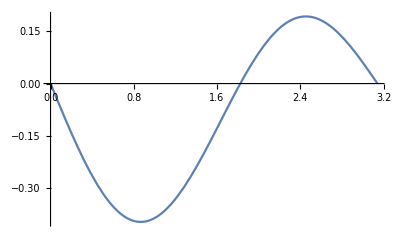

```mathematica
Plot[signalXS[ArcTan[3.4/6.8],β],{β,0,π}]
```

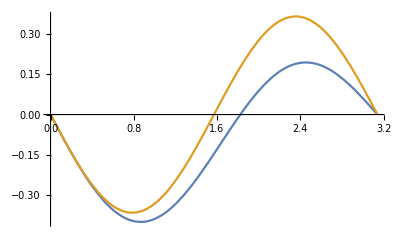

```mathematica
Plot[{signalXS[ArcTan[3.4/6.8],β],(signalXpm[ArcTan[3.4/6.8], β]+signalXmp[ArcTan[3.4/6.8], β])/2},{β,0,π}]
```

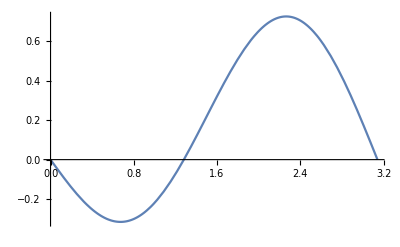

```mathematica
Plot[signalXpm[ArcTan[3.4/6.8], β],{β,0,π}]
```

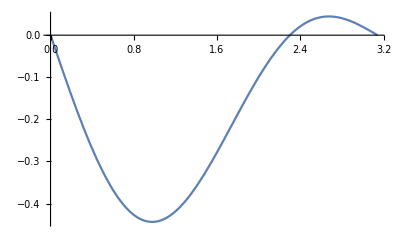

```mathematica
Plot[signalXmp[ArcTan[3.4/6.8], β],{β,0,π}]
```